```mathematica
Clear["`*"]
color = {RGBColor[1, 31/255, 91/255], RGBColor[0, 41/51, 36/85], RGBColor[0, 154/255, 74/85], RGBColor[35/51, 88/255, 62/85],
RGBColor[1, 66/85, 2/17], RGBColor[242/255, 133/255, 2/15],RGBColor[0, 92/255, 171/255]};
```

# Negative Stiffness Model

### Transfer Function Math

```mathematica
(*First, we define a multiply function that can take a list of data or an analytic function and multiply them together
data input: must be 2×n array, frequency in first row, values in second*)
tfMult[input_]:=(
Module[{tFuncs, ff,i, prod, tFuncs2},
tFuncs  = input;
tFuncs2 = Table[If[ArrayQ[tFuncs⟦i⟧]==True,
Interpolation[Transpose[tFuncs⟦i⟧]],
tFuncs⟦i⟧]
,{i, Length[tFuncs]}];
ff= Table[tFuncs2⟦i⟧[#] &/.i->j, {j, Length[tFuncs2]}];
prod = ff⟦1⟧;
For[i=1, i≤Length[ff]-1, i++,
prod=Times[prod, ff⟦i+1⟧];
];
Through[(prod)[#]] &])//Quiet
```

### Chamberlain Vibrational Noise

```mathematica
Module[{bins, pixels, unlogch,y},
bins = {0,1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {0,200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
unlogch[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
chNoise = {bins,Table[unlogch[pixels⟦i⟧],{i, 1, Length[pixels]}]};
resultantNoise[x_] := 
Transpose[{chNoise⟦1,2;;-1⟧,Table[(chNoise⟦1,i⟧//x)*chNoise⟦2,i⟧,{i,2,Length[chNoise⟦1⟧-1]}]}];
Options[pltNoise]={"PlotStyle"->ColorData[1, "ColorList"]⟦1⟧};
pltNoise[x_, OptionsPattern[]] := ListStepPlot[x, ScalingFunctions->{"Log10", "Log10"}, PlotLabel->"Attenuated Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Vibrational Amplitude (m_rms)"},PlotStyle->OptionValue["PlotStyle"],PlotRange->{{1.25,100},Automatic}];
];
```

find factor such that vibration is less than a pm, find largest one and return both factor and freq

### Defining Transfer Functions

#### Spring-Mass-Damper System

The transfer function is taken from [1].

[1] https://aip.scitation.org/doi/pdf/10.1063/1.1139507

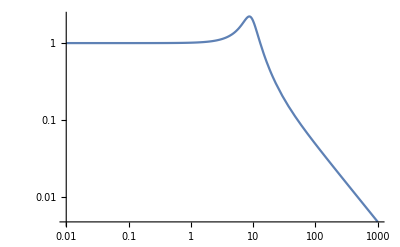

```mathematica
Options[tfSpring] = {"k_spring"->10000, "m_STM"-> 3, "c_spring" ->10 };
tfSpring[OptionsPattern[]][f_]:=(
With[{k = OptionValue["k_spring"], m = OptionValue["m_STM"], c = OptionValue["c_spring"]},
ω0 =√(k/m);
γ=c/2m;
(√(4 γ^2(2π f)^6+(ω0^4-ω0^2(2π f)^2+4 γ^2(2π f)^2)^2))/((ω0^2-(2π f)^2)^2+4 γ^2(2π f)^2)//N]
);
LogLogPlot[tfSpring[ "k_spring"->10000, "c_spring"->10, "m_STM"->3][x],{x,0.01, 1000}]
```

#### Air Leg System

Data comes from the spec sheet in Ref [1].

[1] https://www.newport.com/p/S-2000A-428

-Graphics-

```mathematica
Module[{dataim, pixelData, x, alData,beg},dataim = ImageData[Import["C:\\Users\\freem\\Documents\\GitHub\\MinusKModelling\\Resources\\legs_vert_transf2.bmp"]];
pixelData={};
For[j=1, j≤Dimensions[dataim]⟦2⟧, j++,
x={};
For[i =1 , i≤ Dimensions[dataim]⟦1⟧, i++,
dataim⟦i,j⟧ = dataim⟦i,j,1⟧;
If[dataim⟦i, j⟧≠ 1.,
x = Append[x, i];
];
];
pixelData=Append[pixelData,{j,353-Mean[x]}];
];
alData ={N[0.8*Power[10,Log10[30/0.8]/462*Transpose[pixelData]⟦1⟧]],N[Power[10,4/353 Transpose[pixelData]⟦2⟧-3]]};
beg[f_]:=With[{ω0 =7,γ=0.7},
(√(4 γ^2(2π f)^6+(ω0^4-ω0^2(2π f)^2+4 γ^2(2π f)^2)^2))/((ω0^2-(2π f)^2)^2+4 γ^2(2π f)^2)//N];
tfAirLeg[x_]=Piecewise[{{Interpolation[Transpose[alData]][x], 0.8<x≤30}, {10^-0.91 1/(x-10)^1.6, x>30}, {beg[x], 0.8≥x}}];
]
```

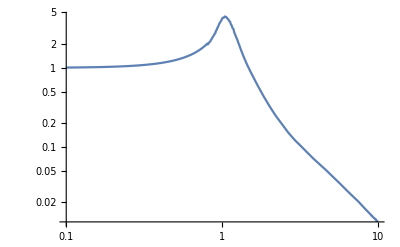

```mathematica
LogLogPlot[tfAirLeg[x], {x, 0.1,10}]
```

#### STM Stiffness

-Graphics-

[1] https://ieeexplore.ieee.org/stamp/stamp.jsp?tp=&arnumber=5390193

```mathematica
tfSTM[f_]:=With[{f0=3000,Q1 = 30},Abs[1-(1+ⅈ((f / f0)/Q1))/((1-( f / f0)^2)+ⅈ (f / f0)/Q1)]];
```

#### Negative Stiffness System - No Composites

```mathematica
Options[tNSS]={"Hysteresis"->False, "kh"->2, "kv"->1,"M"->1, "c1"->0.04,"c2"->0.1 , "L"->0.05, "Bounds"->{0.001, 100}, "PointsPerDecade"->100, "kspr"->200, "cspr"-> 20};
tNSS[inp_,Ze_,OptionsPattern[]]:=Block[{C1 = OptionValue["c1"],C2 = OptionValue["c2"], m = OptionValue["M"], Kv = OptionValue["kv"], Kh=OptionValue["kh"] ,ℒ =OptionValue["L"] ,min = OptionValue["Bounds"]⟦1⟧, max=OptionValue["Bounds"]⟦2⟧,pPD=OptionValue["PointsPerDecade"], ks = OptionValue["kspr"], cs = OptionValue["cspr"],Ω,δqzs,ω0,λ,ze,A,cosθ,T, ζ1, ζ2, tdata, tdataI, tdataII, tdataIII, params, output, string, pltspr, data, ndata, pltcha, cdata, ω0spr, γspr,sprtransf1, logRange,bins, pixels,unlogch,y,minTemp, maxTemp,bI, bII,iNSSfun,NSSdata,},
logRange[l_,u_,n_]:=Table[-(u-l)Log10[i]/Log10[n]+u,{i,n}];
data = logRange[0.001, 100, 2000];

bins = {0,1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {0,200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
unlogch[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
cdata = {bins,Table[unlogch[pixels⟦i⟧],{i, 1, Length[pixels]}]};
ζ1 = C1/(2 m ω0);
ζ2 = C2/(2m ω0);
ω0 = √(Kv/m);
δqzs = 2/(Kh/Kv);
λ = (2-δqzs)/(8 δqzs);
ze[Ω_]:=If[Dimensions[Ze]=={},
 Ze/ℒ,
 Piecewise[
Join[{{Ze⟦2,1⟧,0≤(Ω*ω0)/(2π)<(Ze⟦1, 2⟧+Ze⟦1, 1⟧)/2}},
Table[{Ze⟦2,i⟧,(Ze⟦1, i⟧+Ze⟦1, i-1⟧)/2≤(Ω*ω0)/(2π)<(Ze⟦1, i+1⟧+Ze⟦1, i⟧)/2 }, {i, 2, Length[Ze⟦2⟧]-1}]], Ze⟦2,-1⟧]
];
A[Ω_]:= A/.NSolve[(2ζ1 A Ω+1/8 ζ2 A^3 Ω+1/64 ζ2 A^5 Ω)^2+(3/4 λ A^3-A Ω^2)^2==ze[Ω]^2 Ω^4,A,PositiveReals];
cosθ[Ω_]:= (3/4 λ A[Ω]^3-A[Ω] Ω^2)/(ze[Ω ] Ω^2);
T[f_]:= √((A[(2π f)/ω0]/ze[(2π f)/ω0])^2+2 (A[(2π f)/ω0]/ze[(2π f)/ω0])cosθ[(2π f)/ω0]+1);
logRange[l_,u_,n_]:=Table[-(u-l)Log10[i]/Log10[n]+u,{i,1, n}];
data={};
For[i =1, 10^i*min<10* max, i++,
minTemp= 10^(i-1)min;
maxTemp=10^i min;
ndata=Reverse[logRange[minTemp, maxTemp, pPD]];
data = Join[data,ndata];
];
data=Reverse[DeleteDuplicates[data]];

If[OptionValue["Hysteresis"]==True,
tdata=Reverse[Table[{data⟦i⟧,T[data⟦i⟧]}, {i, Length[data]}]];
(*divide the data into III regions*)
(*Find bounds:*)
bI=1;
bII = Length[tdata];
For[i = 1, i≤Length[tdata], i++,
If[Length[tdata⟦i,2⟧]>1,
bI=i;
Break[];
];
];
For[i = Length[tdata], i≥1, i--,
If[Length[tdata⟦i,2⟧]>1,
bII=i;
Break[];
];
];

(*region I*)
tdataI = Table[{tdata⟦i,1⟧, tdata⟦i,2,-1⟧},{i, bII}];
If[bII!=Length[tdata],
(*region II*)
tdataII =Reverse[Table[{tdata⟦i,1⟧, tdata⟦i,2,2⟧},{i, bI,bII}]];

(*region III*)
tdataIII = Table[{tdata⟦i,1⟧, tdata⟦i,2,1⟧},{i, bI,Length[tdata]}];
tdata=Catenate[{tdataI,tdataII,tdataIII}];
,
tdata = tdataI;
];
,
tdata=Table[{data⟦i⟧,T[data⟦i⟧]⟦-1⟧}, {i, Length[data]}];
];
ω0spr =√(ks/m);
γspr=cs/(2 m ω0spr);
sprtransf1[f_]:=(√(4 γspr^2(2π f)^6+(ω0spr^4-ω0spr^2(2π f)^2+4 γspr^2(2π f)^2)^2))/((ω0spr^2-(2π f)^2)^2+4 γspr^2(2π f)^2);
tdata = Transpose[tdata];
tdata ={ tdata⟦1⟧,tdata⟦2⟧*Table[sprtransf1[tdata⟦1,i⟧],{i, 1, Length[tdata⟦1⟧]}]};
tdata = Transpose[tdata];
output={};
If[inp == "all", string = "plot, data, params, spring, chamb", string=inp];
If[StringContainsQ[string, "plot"] == True,
output=Append[output,ListPlot[tdata, Joined->True, PlotLabel->"Transfer Functions", AxesLabel->{"Freq (Hz)", "Attenuation"}, PlotRange->{{0.1, 100},{10^-5,10}},PlotStyle->color⟦1⟧, ScalingFunctions->{"Log10", "Log10"}]];
];
If[StringContainsQ[string, "data"] == True,
	output=Append[output,Transpose[tdata]]];
If[StringContainsQ[string, "params"] == True,
	params= {"ω_0 → "<>ToString[ω0//N],"δ_qzs → "<>ToString[δqzs//N],"ζ_1 → "<>ToString[ζ1//N],"ζ_2 → "<>ToString[ζ2//N]};
	output=Append[output,params]];
If[StringContainsQ[string,"spring"],
pltspr=LogLogPlot[sprtransf1[f], {f, 0.01, 100}, PlotStyle->Red,PlotRange->{{0.1, 30},{0.001,100}}];
output=Append[output,pltspr]];
If[StringContainsQ[string,"chamb"],
iNSSfun=Interpolation[NSSdata];
pltcha = ListStepPlot[Transpose[{bins⟦2;;-1⟧,iNSSfun[bins⟦2;;-1⟧]*cdata⟦2,2;;-1⟧}], PlotLabel->"Attenuated Vibrational Noise Spectrum", AxesLabel->{"Freq (Hz)", "Vibrational Amplitude (m_rms)"},PlotRange->{{1.25,100},{10^-16,10^-7}}, PlotStyle->color⟦1⟧,ScalingFunctions->{"Log10", "Log10"}];
output=Append[output,pltcha]];
output
]
tfNSS =tNSS["data",chNoise,Bounds->{0.1, 10^5},c1->10, c2->440,kh->500,kv->1500,M->10, L->0.15,Hysteresis->True, PointsPerDecade->100, kspr->1000, cspr->440]⟦1⟧;
```

#### Negative Stiffness System - Composites I

-Graphics-

```mathematica
Module[{dataim, pixelData, x, qzsData,beg},dataim = ImageData[Import["C:\\Users\\freem\\Documents\\GitHub\\MinusKModelling\\Resources\\qzs.bmp"]];
Clear[i,j];
pixelData={};
For[j=1, j≤Dimensions[dataim]⟦2⟧, j++,
x={};
For[i =1 , i≤ Dimensions[dataim]⟦1⟧, i++,
dataim⟦i,j⟧ = dataim⟦i,j,1⟧;
If[dataim⟦i, j⟧≤0.9,
x = Append[x, i];
];
];
pixelData=Append[pixelData,{j,-Mean[x]+Dimensions[dataim]⟦1⟧}//N];
];
pixelData = Transpose[pixelData];
qzsData = {(100*pixelData⟦1⟧)/(Dimensions[dataim]⟦2⟧),10^(((60*pixelData⟦2⟧)/(Dimensions[dataim]⟦1⟧)-20)/10)};
tfQZSI = Interpolation[Transpose[qzsData]];
]
```

tan δ = 2 ζ, where ζ is the damping constant, also called the damping coefficient, also called the quality factor, also called the loss factor, because why wouldn’t you need 5 words to describe the same goddamn thing

### Implementations

#### Spring and Air Legs

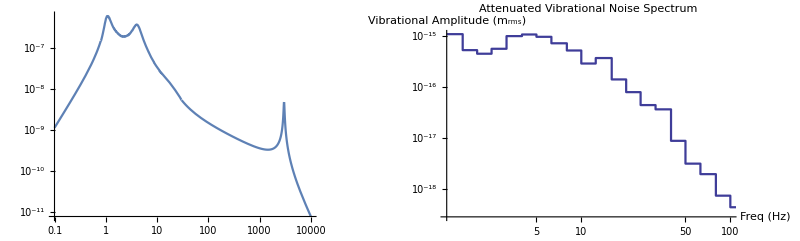

```mathematica
tfAirLegSpring=tfMult[{tfAirLeg,tfSpring["k_spring"->2000, "c_spring"->3, "m_STM"->3], tfSTM}];
GraphicsRow[{LogLogPlot[tfAirLegSpring[x], {x, 0.1, 10000}, PlotRange->All],
pltNoise[resultantNoise[tfAirLegSpring]]}]
```

#### Negative Stiffness System

- The particular system implemented is a “quasi-zero stiffness” device from Ref [1]. It is roughly the same design as the device in Ref [2] (theory was too approximate {?}), and could be easily converted to that design if needed. I also added a second stage to the device.
 - Compared to the air legs & spring model, this model shows a ~1 order of magnitude decrease in (effective) resonance frequency, and a ~1 order of magnitude increase in attenuation for low frequencies. The dB/decade @ ≳10
 Hz is worse for this model compared to the air legs & spring model, however putting the device in series with another spring or air legs could make the dB/decade better (possibly at the expense of some low-frequency attenuation).
 - All parameters (e.g., damping coefficients, spring constants, etc) are stable to within an order of magnitude (at least).
 - The vertical damper must be an eddy current damper, as traditional dampers provide too much damping. Links to dampers: C_1→ ([3],[4]), C_2→ [5]
-Graphics--Graphics-

[1] https://link.springer.com/content/pdf/10.1007/s11071-016-3188-0.pdf
 [2] https://www.sciencedirect.com/science/article/pii/S0020740313000726
 [3] https://www.honeybeerobotics.com/wp-content/uploads/2019/10/Avior-Damper-Catalog.pdf
 [4] https://www.sciencedirect.com/science/article/pii/S0022460X08001399
 [5] https://www.springfixlinkages.com/en/catalog/air-cylinders/dashpots/push-pull-dampers/l4572

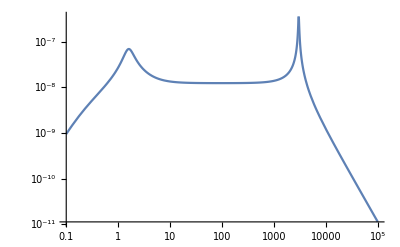

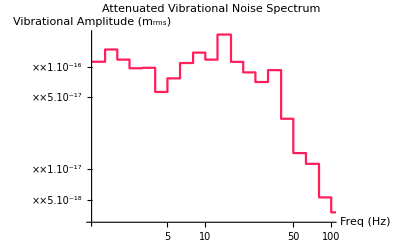

```mathematica
tfNSSSTM=tfMult[{tfNSS, tfSTM}];
LogLogPlot[tfNSSSTM[x],{x, 0.1, 10^5}, PlotRange->All]
Show[pltNoise[resultantNoise[tfNSSSTM], "PlotStyle"->color⟦1⟧],pltNoise[Transpose[chNoise]] ]
```

#### QZS Composite I

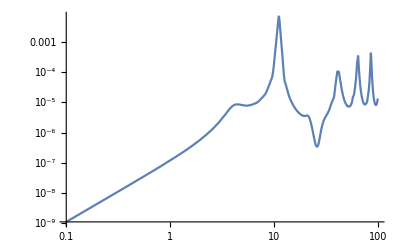

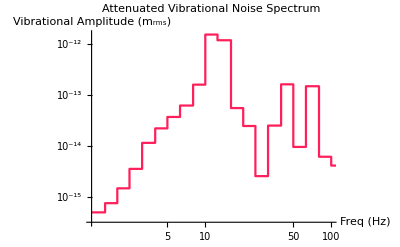

```mathematica
tfQZSISTM=tfMult[{tfQZSI, tfSpring["k_spring"->2000, "c_spring"->3, "m_STM"->3],tfSTM}];
LogLogPlot[tfQZSISTM[x],{x, 0.1, 100}, PlotRange->All]
Show[pltNoise[resultantNoise[tfQZSISTM], "PlotStyle"->color⟦1⟧],pltNoise[Transpose[chNoise]] ]
```